## Basic idea as presented in Göttingen (01/03/2024)

```mathematica
M = 4;

f[oi_,oj_,β_]:=(-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M)

p = 0.5;
oAchange[oA_,oB_,β_]:= (1-p)f[oA,oA,β]+ p f[oA,oB,β]
oBchange[oA_,oB_,β_]:= (1-p)f[oB,oB,β]+ p f[oB,oA,β]

vmin=-1.2;
vmax = 1.2;
Manipulate[
Show[StreamPlot[{oAchange[oA,oB,β], oBchange[oA,oB,β]},{oA,vmin,vmax},{oB,vmin,vmax},FrameLabel->{"opinion in group A","opinion in group B"},ImageSize->Large,BaseStyle->{Large,FontFamily->"Helvetica",Italic}],
ContourPlot[{oAchange[oA,oB,β]==0, oBchange[oA,oB,β]==0},{oA,vmin,vmax},{oB,vmin,vmax},ContourStyle->Thick]],
{{β,0.0},0,4.2,Appearance-> "Labeled"}
]
```

```mathematica
p=.;
M = .;
Simplify[oAchange[oA,oB,β]]
FullSimplify[oBchange[oA,oB,β]]
```

((-oA+oB) p+(1+oA^2 (-1+p)-oA oB p) Tanh[(oA β)/2])/(4 M)

((oA-oB) p+(1+oB^2 (-1+p)-oA oB p) Tanh[(oB β)/2])/(4 M)

## Generalized Model (08/03/2024)

## Parameters and IRF

```mathematica
β=.; (* confirmation bias *)
p=.; (* group coupling *)
θ=.; (* idiosyncratic noise *)
ρ=.; (* state-dependent noise *)

M = 4;
f[oi_,oj_,β_,θ_]:=(1-θ)((-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M))-θ oi
```

## Opinion change in a two-group setting

```mathematica
oAchange[oA_,oB_,β_,p_,θ_,ρ_]:= (1-ρ)( (1-p)f[oA,oA,β,θ]+ p f[oA,oB,β,θ] )  + ρ f[oA,0,β,θ]
oBchange[oA_,oB_,β_,p_,θ_,ρ_]:= (1-ρ)( (1-p)f[oB,oB,β,θ]+ p f[oB,oA,β,θ] ) + ρ f[oB,0,β,θ]

vmin=-1.2;
vmax = 1.2;
Manipulate[
Show[StreamPlot[{oAchange[oA,oB,β,p,θ,ρ], oBchange[oA,oB,β,p,θ,ρ]},{oA,vmin,vmax},{oB,vmin,vmax},FrameLabel->{"opinion in group A","opinion in group B"},ImageSize->Large,BaseStyle->{Large,FontFamily->"Helvetica",Italic},StreamScale->0.08,StreamStyle->Automatic,StreamPoints->200,GridLines->Automatic],
ContourPlot[{oAchange[oA,oB,β,p,θ,ρ]==0, oBchange[oA,oB,β,p,θ,ρ]==0},{oA,vmin,vmax},{oB,vmin,vmax},ContourStyle->Thick]],
{{β,3.4},0,4,Appearance-> "Labeled"},
{{p,0.5},0,1.0,Appearance-> "Labeled"},
{{θ,0.0},0,0.2,Appearance-> "Labeled"},
{{ρ,0.0},0,1.0,Appearance-> "Labeled"}
]
```

## Temporal evolution (random graph, no noise)

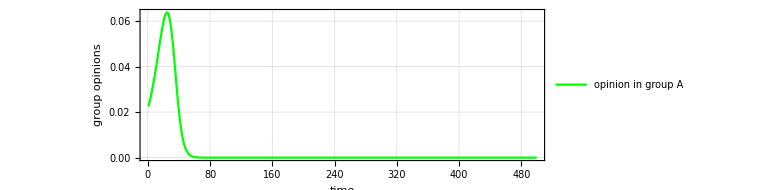

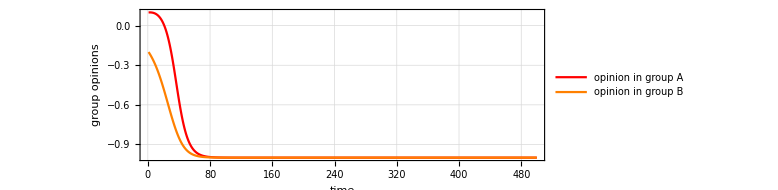

```mathematica
M = 4;
f[oi_,oj_,β_]:=(-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M)
p = 0.5;
oAchange[oA_,oB_,β_]:= (1-p)f[oA,oA,β]+ p f[oA,oB,β]
oBchange[oA_,oB_,β_]:= (1-p)f[oB,oB,β]+ p f[oB,oA,β]


(*β = 2.602;
oA = 0.4;
oB = -0.4;*)
β = 3.1;
oA = 0.1;
oB = -0.2;

T = 500; (* number of iterations *)   
Oobs = Table[{0,0},{i,T}];

For[i=1,i<=T,i++,

Oobs[[i]][[1]]=oA;
Oobs[[i]][[2]]=oB;

oA =oA+oAchange[oA,oB,β];
oB = oB+ oBchange[oA,oB,β];

]

ListPlot[1/2Variance[Transpose[Oobs]],PlotStyle->{Red,Orange,Blue,Green},Joined->True,PlotRange->All,PlotLegends->{"opinion in group A","opinion in group B"},AspectRatio->0.33,Frame->True,FrameLabel->{"time","group opinions"},BaseStyle->{Large,FontFamily->"Helvetica",Italic},ImageSize->Large,GridLines->Automatic]
ListPlot[Transpose[Oobs],PlotStyle->{Red,Orange,Blue,Green},Joined->True,PlotRange->All,PlotLegends->{"opinion in group A","opinion in group B"},AspectRatio->0.33,Frame->True,FrameLabel->{"time","group opinions"},BaseStyle->{Large,FontFamily->"Helvetica",Italic},ImageSize->Large,GridLines->Automatic]
```

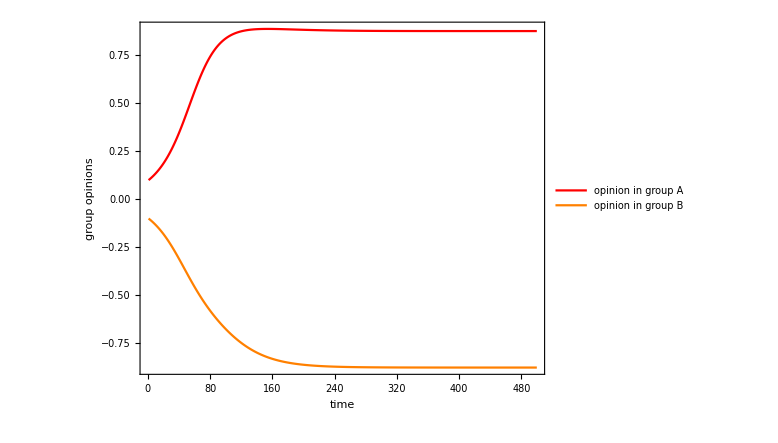

## Bifurcation analysis (08/03/2024)

## Basic model without noise

```mathematica
M = 4;
f[oi_,oj_,β_]:=(-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M)
p = 1/2;
oAchange[oA_,oB_,β_]:= (1-p)f[oA,oA,β]+ p f[oA,oB,β]
oBchange[oA_,oB_,β_]:= (1-p)f[oB,oB,β]+ p f[oB,oA,β]
```

```mathematica
oA =.;
oB=.;
β =4;
NSolve[{oAchange[oA,oB,β] == 0,oBchange[oA,oB,β]==0},{oA,oB},Reals]
```

{{oA→-0.979641,oB→0.34389},{oA→-0.957504,oB→0.957504},{oA→-0.34389,oB→0.979641},{oA→0,oB→0},{oA→0.34389,oB→-0.979641},{oA→0.957504,oB→-0.957504},{oA→0.979641,oB→-0.34389},{oA→1.,oB→1.},{oA→-1.,oB→-1.}}

```mathematica
β =1;
SolveValues[{oAchange[oA,oB,β] == 0&&oBchange[oA,oB,β]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals]
```

{{-1,-1},{0,0},{1,1}}

```mathematica
(*β =.;
Solve[{oAchange[oA,oB,β] == 0&&oBchange[oA,oB,β]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals]*)
```

```mathematica
samples=100;
βmax = 6;
sols = Table[NSolveValues[{oAchange[oA,oB,βmax sample/samples] == 0&&oBchange[oA,oB,βmax sample/samples]==0&&oA>=-1&&oA<=1&&oB>=-1&&oB<=1},{oA,oB},Reals],{sample,1,samples,1}
];
```

```mathematica
sols[[;;,;;,1]];
```

```mathematica
(*solsP1 = Table[CenterArray[sols[[;;,;;,1]], {Inherited,9},0],{sample,1,samples,1}]*)
CenterArray[sols[[30]],9]
```

{{0.,0.},{0.,0.},{0.,0.},{-1.,-1.},{0.,0.},{1.,1.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
(*solsP1 = Table[PadRight[sols[[sample]],9,{{0,0}}],{sample,1,samples,1}]*)
solsP1 = Table[CenterArray[sols[[sample]], 9,{{0,0}}],{sample,1,samples,1}];
solsP2 = Table[CenterArray[sols[[sample]], 9,{{-1,-1},{0,0},{1,1}}],{sample,1,samples,1}];
solsP3 = Table[CenterArray[sols[[sample]], 9,sols[[sample]]],{sample,1,samples,1}];
(*solsP3 = Table[PadRight[sols[[sample]], 9,sols[[sample]]],{sample,1,samples,1}];*)
(*solsP4 = Table[ArrayPad[sols[[sample]], (9-Length[sols[[sample]]])/2],{sample,1,samples,1}];*)
TableForm[solsP3];
```

```mathematica
Export["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/data.csv",sols,"CSV"]
```

/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/data.csv

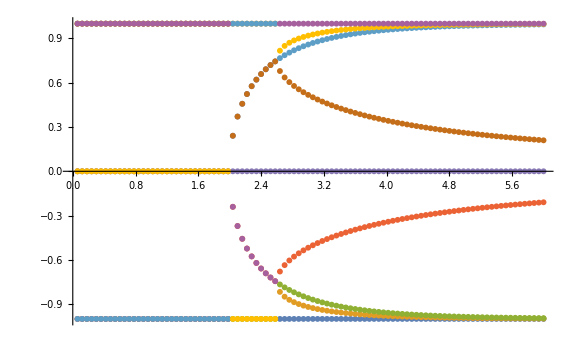

```mathematica
ListPlot[Transpose[solsP3[[;;,;;,1]]],Joined->False,ImageSize->Large,DataRange->{βmax /samples,βmax}]
```

```mathematica
solsP3[[samples,;;,;;]]
Variance[Transpose[sols[[samples,;;,;;]]]]
pd1 = Table[Variance[Transpose[sols[[sample,;;,;;]]]],{sample,1,samples,1}];
pd2 =  Table[PadRight[1/2 Variance[Transpose[sols[[sample,;;,;;]]]],9],{sample,1,samples,1}];
```

{{-1.,-1.},{-0.997819,0.209839},{-0.994902,0.994902},{-0.209839,0.997819},{0.,0.},{0.209839,-0.997819},{0.994902,-0.994902},{0.997819,-0.209839},{1.,1.}}

{0.,0.729219,1.97966,0.729219,0.,0.729219,1.97966,0.729219,0.}

```mathematica
Export["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/data.csv",pd2,"CSV"]
```

/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/data.csv

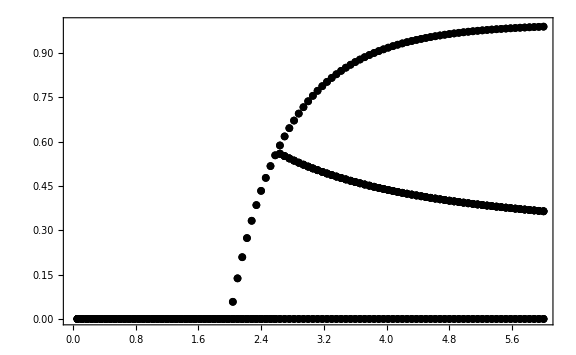

```mathematica
ListPlot[Transpose[pd2],Joined->False,ImageSize->Large,DataRange->{βmax /samples,βmax},Frame->True,PlotRange->{Automatic,{0,1}},PlotStyle->{Black},PlotMarkers->{Graphics[{Disk[]}],8}]
```

```mathematica
simdata =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/fnvarO.mat"][[1]];
```

```mathematica
(*simdata//MatrixForm
Mean[simdata]//MatrixForm*)
```

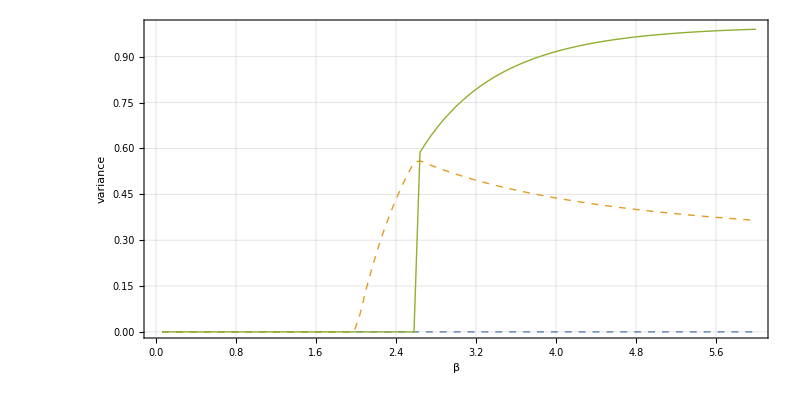

```mathematica
gmf = ListPlot[Transpose[pd2[[;;,1;;3]]],Joined->True,ImageSize->Large,DataRange->{βmax /samples,βmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,AspectRatio->1/2,PlotStyle->{{Dashed,Thick},{Dashed,Thick},Thick},(*PlotMarkers->{Graphics[{Disk[]}],8},*)Frame->True,FrameLabel->{"β","variance"},BaseStyle->{Large,FontFamily->"Helvetica"},ImageSize->800,GridLines->Automatic];

simfnR =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/fnvarR.mat"][[1]];
simfnO =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/fnvarO.mat"][[1]];
(*simmxR =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/mxvarR.mat"][[1]];
simmxO =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/mxvarO.mat"][[1]];*)

sim1000R =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/T1000R.mat"][[1]];
sim3000R =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/T3000R.mat"][[1]];
sim5000R =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/T5000R.mat"][[1]];

sim1000O =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/T1000O.mat"][[1]];
sim3000O =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/T3000O.mat"][[1]];
sim5000O =Import["/Users/seven/data/HiDrive/users/svenbanisch/Projekte/ComputationalSocialScience/Models/ArgumentModels/2023-11-ModelReduction/MATdata/T5000O.mat"][[1]];


gsimpol10000R=ListPlot[{Mean[simfnR],Mean[sim1000R],Mean[sim3000R],Mean[sim5000R]},Joined->True,ImageSize->Large,DataRange->{0,βmax},Frame->True,PlotRange->{Automatic,{0,1}}];

gsimpol10000O=ListPlot[{Mean[simfnO],Mean[sim1000O],Mean[sim3000O],Mean[sim5000O]},Joined->True,ImageSize->Large,DataRange->{0,βmax},Frame->True,PlotRange->{Automatic,{0,1}}];

gsim=ListPlot[{Mean[simfnR],Mean[simfnO]},Joined->True,ImageSize->Large,DataRange->{0,βmax},Frame->True,PlotRange->{Automatic,{0,1}}];

(*gsimfnO=ListPlot[Mean[simfnO],Joined->False,ImageSize->Large,DataRange->{0,βmax},Frame->True,PlotRange->{Automatic,{0,1}}];*)

(*Show[gmf,gsimpol1000,gsimpol5000]*)
Show[gmf,ImageSize->800]
```

```mathematica
gmf = ListPlot[Transpose[pd2],Joined->True,ImageSize->800,DataRange->{βmax /samples,βmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,AspectRatio->1/2,PlotStyle->Black,(*PlotMarkers->{Graphics[{Disk[]}],5},*)Frame->True,FrameLabel->{"β","variance"},BaseStyle->{Large,FontFamily->"Helvetica"},ImageSize->Large,GridLines->Automatic];

(*Define a cross marker*)crossMarker=Graphics[{Red,Thickness[0.002],Line[{{-0.005,0},{0.005,0}}],Line[{{0,-0.005},{0,0.005}}]}];
timesMarker=Graphics[{Red,Thickness[0.02],Line[{{-0.0005,-0.0005},{0.0005,0.0005}}],Line[{{-0.0005,0.0005},{0.0005,-0.0005}}]}];


sim = ListPlot[simfnR,PlotStyle->{RGBColor[0.4,0.4,0.8]},Joined->False,ImageSize->Large,DataRange->{βmax /samples,βmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,PlotMarkers->"*"];

simO = ListPlot[simfnO,PlotStyle->Orange,Joined->False,ImageSize->Large,DataRange->{βmax /samples,βmax},Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,PlotMarkers->"×"];


Show[gmf,sim]
```

-Graphics-

```mathematica
Variance[{1,-1}]
```

2

{0,0,0,0,0,0.65857,-0.586179,-0.467738,-0.39545,-0.34389}

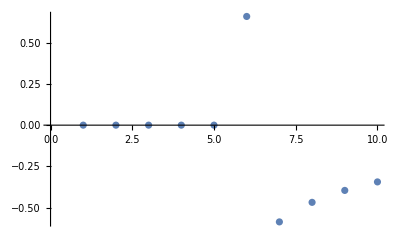

```mathematica
fpoA = Table[sols[[sample,4,1]],{sample,1,samples,1}] 
ListPlot[fpoA]

(*For[s = 1,s<=samples,s++,

l = Length[sols[[s]]]];



]*)
```

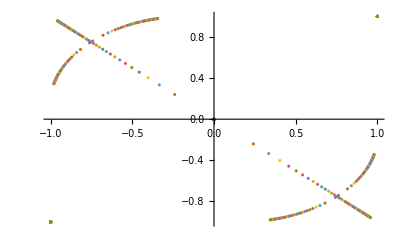

```mathematica
ListPlot[sols]
```

```mathematica
first = Table[sols[[sample,1]][[1]],{sample,1,samples,1}]
second = Table[sols[[sample,2]][[1]],{sample,1,samples,1}]
third = Table[sols[[sample,3]][[1]],{sample,1,samples,1}]
```

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

{0,0,0,0,0,-0.65857,-0.881652,-0.941014,-0.966277,-0.979641}

{1.,1.,1.,1.,1.,0,-0.814529,-0.890643,-0.932718,-0.957504}

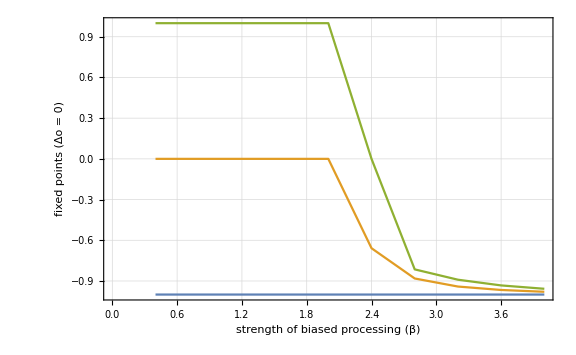

```mathematica
ListPlot[{first,second,third},Joined->True,Frame->True,DataRange->{0+βmax/samples,βmax},BaseStyle->{FontSize->18,FontFamily->"Calibri"},FrameLabel->{Style["strength of biased processing (β)",18,Italic],Style["fixed points (Δo = 0)",18,Italic]},ImageSize->Large,GridLines->Automatic]
```

```mathematica
sols
```

NSolveValues::ratnz: NSolveValues was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolveValues::svars: Equations may not give solutions for all "solve" variables.

ReplaceAll::reps: {oB,oB} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSolveValues::ratnz: NSolveValues was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ReplaceAll::reps: {-1.,-1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0,0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NSolveValues::ratnz: NSolveValues was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolveValues::ratnz will be suppressed during this calculation.

{{{oA,oB}/.{ConditionalExpression[oB, -1.≤oB≤1.],oB}},{{oA,oB}/.{-1.,-1.},{oA,oB}/.{0,0},{oA,oB}/.{1.,1.}},{{oA,oB}/.{-1.,-1.},{oA,oB}/.{0,0},{oA,oB}/.{1.,1.}},{oA,oB}/.NSolveValues[{1/32 (1-oA^2) Tanh[0.3 oA]+1/32 (-oA+oB+(1-oA oB) Tanh[0.3 oA])==0&&1/32 (1-oB^2) Tanh[0.3 oB]+1/32 (oA-oB+(1-oA oB) Tanh[0.3 oB])==0&&oA≥-1&&oA≤1&&oB≥-1&&oB≤1},{oA,oB},ℝ],{{oA,oB}/.{-1.,-1.},{oA,oB}/.{0,0},{oA,oB}/.{1.,1.}},{{oA,oB}/.{-1.,-1.},{oA,oB}/.{0,0},{oA,oB}/.{1.,1.}}}

```mathematica
fpneg:=Table[{oA,oB}/.FindRoot[oAchange[oA,oB,β],{o,-4}],{β,0,1.2,0.01}]
fppos:=Table[o/.FindRoot[expChangeCont[o,β],{o,4}],{β,0,1.2,0.01}]
fpzero:=Table[o/.FindRoot[expChangeCont[o,β],{o,0}],{β,0,1.2,0.01}]
fp={fpzero,fpneg,fppos};
fpg1=ListPlot[fp,Joined->True,Frame->True,DataRange->{0,1.2},BaseStyle->{FontSize->18,FontFamily->"Calibri"},FrameLabel->{Style["strength of biased processing (β)",18,Italic],Style["fixed points (Δo = 0)",18,Italic]},ImageSize->Large,GridLines->Automatic]
```